一个宇宙学的例子-Cosmological Solution


由以上的状态方程和连续性方程容易得到

```mathematica
NIntegrate[1/(√(0.31*(1+z)^3)),{z,1000,Infinity}]*2997.92
```

340.371

```mathematica
Subscript[Ω, Λ]=0.69;
Subscript[Ω, m]=0.31;
Subscript[Ω, γ]=5*10^-5;
H[z_]:= (√(Subscript[Ω, γ](1+z)^4+Subscript[Ω, m](1+z)^3+Subscript[Ω, Λ]))/QuantityMagnitude[UnitConvert[1/Quantity[, "HubbleParameter"],"Gyr"]]
t0=NIntegrate[1/((1+z)H[z]),{z,0,Infinity}]
```

13.8115

NDSolve::ndnum: 在 t == 0. 处碰到一个导数的非数值量.

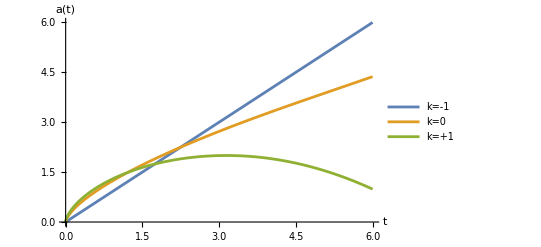

```mathematica
sol=NDSolve[{a'[t]*a[t]==Sqrt[(1+k)*a[t]-k*(a[t])^2],a[0]==0.001},a,{t,0,3.1}]/.{{k->-1},{k->0},{k->1}};
Plot[Evaluate[a[t]/.sol],{t,0,6},
PlotLegends->{"k=-1","k=0","k=+1"},AxesLabel->{"t","a(t)"}]
```

de Sitter Universe - Λ 主导的宇宙

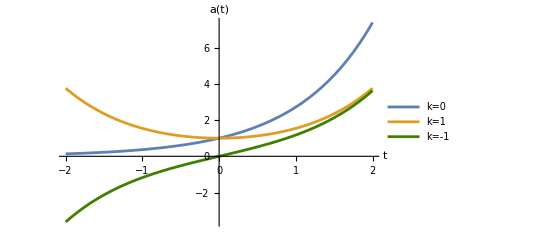

```mathematica
sol1=DSolve[{a'[t]==Sqrt[(a[t])^2-k],a[0]==1},a,t]/.{{k->0},{k->1}};
sol2=DSolve[{a'[t]==Sqrt[(a[t])^2+1],a[0]==0},a,t];
Show[
Plot[Evaluate[a[t]/.sol1],{t,-2,2},PlotLegends->{"k=0","k=1"}],
Plot[Evaluate[a[t]/.sol2],{t,-2,2},PlotLegends->{"k=-1"},PlotStyle->RGBColor[0.25,0.5,0]],
PlotRange->All,
AxesLabel->{"t","a(t)"}
]
```

```mathematica
H0=1/QuantityMagnitude[UnitConvert[1/Quantity[, "HubbleParameter"],"Gyr"]]
```

0.07

NDSolve::ndnum: 在 t == 0. 处碰到一个导数的非数值量.

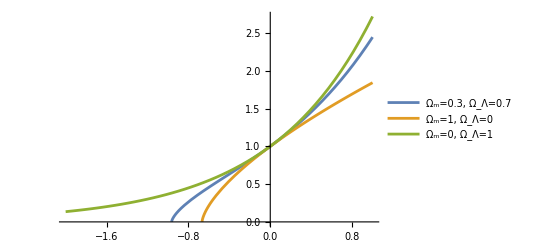

```mathematica
at=NDSolve[{a'[t]==Sqrt[m/a[t]+n*(a[t])^2],a[0]==1},a,{t,-10,10}]/.{{m->0.3,n->0.7},{m->1,n->0},{m->0,n->1}};
Plot[Evaluate[a[t]/.at],{t,-2,1},
PlotLegends->{"Ω_m=0.3, Ω_Λ=0.7","Ω_m=1, Ω_Λ=0","Ω_m=0, Ω_Λ=1"}
]
```

```mathematica
m/a[t]+n*(a[t])^2+(1-m-n)/.{{m->0.3,n->0.7},{m->0.3,n->0},{m->1,n->0},{m->3,n->0}}
```

{0.+0.3/a[t]+0.7 a[t]^2,0.7+0.3/a[t],1/a[t],-2+3/a[t]}

```mathematica
at1=NDSolve[{a'[t]==Sqrt[0.3/a[t]+0.7 a[t]^2],a[0]==1},a,{t,-1,5}];
at2=NDSolve[{a'[t]==Sqrt[0.7+0.3/a[t]],a[0]==1},a,{t,-1,5}];
at3=NDSolve[{a'[t]==Sqrt[1/a[t]],a[0]==1},a,{t,-1,5}];
at4=NDSolve[{a'[t]==Sqrt[-2+3/a[t]],a[0]==1},a,{t,-1,5}];
```

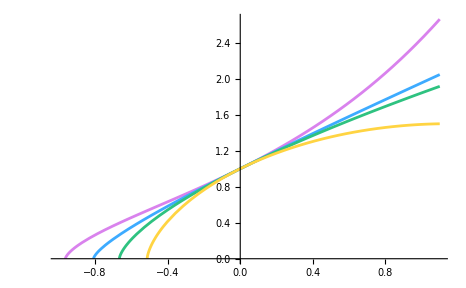

```mathematica
Show[
Plot[Evaluate[a[t]/.at1],{t,-1,1.1},PlotStyle->RGBColor[0.85,0.51,0.93],PlotLegends->Placed[{"Ω_m=0.3, Ω_Λ=0.7, ΛCDM"},{Left,Top}]],
Plot[Evaluate[a[t]/.at2],{t,-1,1.1},PlotStyle->RGBColor[0.24,0.67,1],PlotLegends->Placed[{"Ω_m=0.3, Ω_Λ=0, Open Matter"},{Left,Top}]],
Plot[Evaluate[a[t]/.at3],{t,-1,1.1},PlotStyle->RGBColor[0.18,0.76,0.5],PlotLegends->Placed[{"Ω_m=1, Ω_Λ=0, Flat Matter"},{Left,Top}]],
Plot[Evaluate[a[t]/.at4],{t,-1,1.1},PlotStyle->RGBColor[1,0.83,0.26],PlotLegends->Placed[{"Ω_m=3, Ω_Λ=0, Closed Matter"},{Left,Top}]]
]
```

```mathematica
UnitConvert[Quantity[, "ElectronMass"]Quantity[, "SpeedOfLight"]^2/Quantity[, "BoltzmannConstant"],"Kelvins"]
```

5.92989658×10^9 K

```mathematica
UnitConvert[13.6 Quantity[, "Electronvolts"]/Quantity[, "BoltzmannConstant"],"Kelvins"]
```

157821. K

```mathematica
τ=QuantityMagnitude[UnitConvert[(Quantity[, "ElectronMass"] Quantity[, "SpeedOfLight"]^2)/(2Pi Quantity[, "BoltzmannConstant"])]];
t=QuantityMagnitude[UnitConvert[(13.6 Quantity[, "Electronvolts"])/Quantity[, "BoltzmannConstant"]]];
p=QuantityMagnitude[UnitConvert[Quantity[, "BoltzmannConstant"]/Quantity[, "Electronvolts"]]];
eq=(1-x)/x^2==6*10^-10*(B/0.022)*(2*Zeta[3])/Pi^2(T/τ)^(3/2)Exp[t/T];
REC1=Table[{T*p/.NSolve[eq/.{B->0.01},T][[1]],x},{x,0.001,0.999,0.01}];
REC2=Table[{T*p/.NSolve[eq/.{B->0.1},T][[1]],x},{x,0.001,0.999,0.01}];
REC3=Table[{T*p/.NSolve[eq/.{B->1},T][[1]],x},{x,0.001,0.999,0.01}];
```

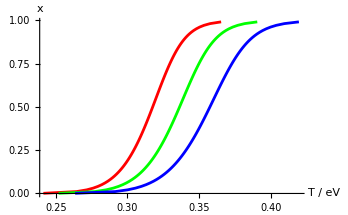

```mathematica
Show[ListLinePlot[REC1,PlotStyle->{Red},PlotLegends->Placed[{"Ω_bh^2=0.01"}, {Left,Top}]],
ListLinePlot[REC2,PlotStyle->{Green},PlotLegends->Placed[{"Ω_bh^2=0.1"}, {Left,Top}]],
ListLinePlot[REC3,PlotStyle->{Blue},PlotLegends->Placed[{"Ω_bh^2=1"}, {Left,Top}]],
AxesLabel->{"T / eV",HoldForm[x]},
PlotRange->All
]
```

```mathematica
UnitConvert[Quantity[, "ProtonMass"] Quantity[, "SpeedOfLight"]^2/Quantity[, "BoltzmannConstant"],"Kelvins"]
UnitConvert[Quantity[, "ElectronMass"] Quantity[, "SpeedOfLight"]^2,"MeV"]
UnitConvert[(Quantity[, "NeutronMass"]-Quantity[, "ProtonMass"])Quantity[, "SpeedOfLight"]^2,"MeV"]
```

1.08881955×10^13 K

0.51099895 MeV

1.2933 MeV

```mathematica
Integrate[SphericalHarmonicY[4,0,θ,ϕ]*Conjugate[SphericalHarmonicY[3,0,θ,ϕ]]Sin[θ],{θ,0,Pi},{ϕ,0,2Pi}]
```

0

```mathematica
Integrate[Exp[-u] u/(√(u^2-a^2)),{u,a,Infinity},Assumptions->{a>0}]
```

a BesselK[1,a]

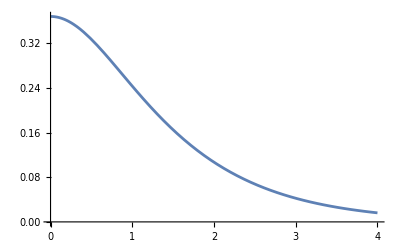

```mathematica
Plot[Exp[-√(y^2+1)],{y,0,4}]
```